# Package testing

## Importando cosas

```mathematica
Get[NotebookDirectory[]<>"DTQW.wl"]
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
<<MaTeX`
```

pdfLaTeX is not found at /usr/bin/pdflatex

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

Click here for documentation on configuring MaTeX.

## Definiendo variables

```mathematica
IndigoC=RGBColor["#729cfc"];
AquaC=RGBColor["#4bd7e5"];
DeepBlueC=RGBColor["#1e2c88"];
```

```mathematica
qlabels=Import[NotebookDirectory[]<>#,{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]]&/@{"../Mariana/Labels_pos.pdf","../Mariana/Labels_prob.pdf"};
clabels=Import[NotebookDirectory[]<>#,{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]]&/@{"../Mariana/Labels_pos.pdf","../Mariana/Labels_probc.pdf"};
plotargs={
BaseStyle->{FontFamily->"LM Roman 12",FontSize->15},
Axes->False,
Frame->True,
Mesh->All,
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,Opacity[0.5]]
};
```

```mathematica
TeXLabel[tlist_List]:=MaTeX[
"\\begin{gathered}\n"<>Fold[
StringJoin[#1,"\\\\\n",#2]&,ToString@StringForm["\\text{``}",#]&/@tlist
]<>"\n\\end{gathered}",
FontSize->14,
Magnification->1.3,
"Preamble"->{"\\usepackage{physics}"}
]
```

```mathematica
rowQW[state_,steps_]:=Module[
{rho,prob},
rho=#.#†&@DTQW2[state,steps];
prob=Abs@Diagonal@MatrixPartialTrace[rho,1,{2,201}]
]
QPascal[state_,steps_]:=Module[
{},
TableForm[#,
TableHeadings->{Range[0,steps],Ket[{#}]&/@ Range[-steps,steps]},
TableSpacing->{2, 2},
TableAlignments->Center,
Label
]&@
(rowQW[state,#][[101-steps;;101+steps]]&/@Range[0,steps])
]
```

```mathematica
(* Poner esto en el paquete *)
PascalRow[n_Integer]:=Riffle[Binomial[n,#]/(2^n)&@Range[0,n],0]
RandomWalkDistribution[n_Integer]:=Transpose[{Range[-n,n],PascalRow[n]}]
```

## Inicializaciones

```mathematica
InitializeDTQW[2,11]
MakeCoin[1/2,0,0];
MakeShift[];
MakeUnitary[];
```

## Resultados

### JAToVec

```mathematica
Shift[JAToVec[{{1/Sqrt[2.],0,0},{ⅈ/Sqrt[2.],1,0}},5]]//MatrixForm
```

(0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.707107+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0.707107 ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ)

```mathematica
JAToVec[{{1/Sqrt[2.],0,1},{ⅈ/Sqrt[2.],1,-1}},5]//MatrixForm
```

(0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.707107+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0.707107 ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ)

### Evolución con matrices de densidad

```mathematica
ev1=Module[
{phi,rho,probs},
phi=VectorState[{{1,0,0}}];
rho=#.#†&@DTQW2[phi,5];
probs=Abs@Diagonal@MatrixPartialTrace[rho,1,{2,11}];
probs
]
```

{0.03125,0.,0.15625,0.,0.125,0.,0.125,0.,0.53125,0.,0.03125}

```mathematica
ev2=Module[
{phi,rho,probs},
phi=DMatrixState[{{1,0,0,0,0}}];
rho=DTQW2[phi,5];
probs=Abs@Diagonal@MatrixPartialTrace[rho,1,{2,11}];
probs
]
```

{0.03125,0.,0.15625,0.,0.125,0.,0.125,0.,0.53125,0.,0.03125}

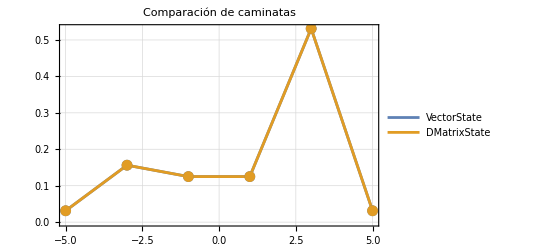

```mathematica
ListLinePlot[{
{Range[-5,5,2],#1[[;;;;2]]}ᵀ,
{Range[-5,5,2],#2[[;;;;2]]}ᵀ
},
plotargs,
PlotLabel->"Comparación de caminatas",
FrameLabel->qlabels,
PlotRange->All,
PlotLegends->{"VectorState","DMatrixState"}
]&[ev1,ev2]
```

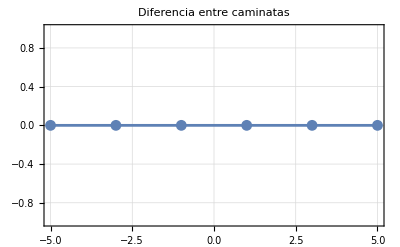

```mathematica
ListLinePlot[{Range[-5,5,2],Abs[#1-#2//Chop][[;;;;2]]}ᵀ,
plotargs,
PlotLabel->"Diferencia entre caminatas",
FrameLabel->qlabels,
PlotRange->All
]&[ev1,ev2]
```